# MintNFT

Mint a non-fungible token (NFT) on a blockchain

## Definition

```mathematica
MintNFT::infun = "Insufficient funds";
MintNFT::maxstr = "Metadata field `1` must be a string with a maximum length of `2` characters";
MintNFT::invval = "Invalid value `1` for `2`, `3` was expected";
MintNFT::blsup = "Not supported for `1` BlockchainBase";
MintNFT::misselem = "Missing key `1` in `2` input association";
MintNFT::errnode= "Node syncing, please try again";
```

```mathematica
Options[MintNFT]={BlockchainBase:>$BlockchainBase,"Preview"->True};
```

```mathematica
MintNFT[nftSpec_?AssociationQ,cryptoSpec_?AssociationQ,opt:OptionsPattern[MintNFT]]:=Catch[Module[{inputAddress,inputAddressData,utxoList,outAmount,timeToLive,policyPubKeyHash,policyScript,policyID,assetName,quantity,mint,metadataAssoc,image,imageIPFS,notebookIPFS,metadata,inputs,outputs,tokensOut, ownerOut,changeOut,txAssoc,create,sign,submit,final,bbase,fee,feeAmount,changeOutMinUTXO,stringExp,source,sourceIPFS,sourceFormat,sourceType},
If[MatchQ[OptionValue[BlockchainBase],Automatic],bbase={"Cardano","Testnet"},bbase=OptionValue[BlockchainBase]];
If[!MatchQ[ToLowerCase[bbase],{"cardano","mainnet"|"testnet"}|"cardano"|{"cardano"}],ResourceFunction["ResourceFunctionMessage"][MintNFT::blsup,bbase];Throw[$Failed]];
If[!BooleanQ[OptionValue["Preview"]],ResourceFunction["ResourceFunctionMessage"][MintNFT::invval,OptionValue["Preview"],"\"Preview\" option","a PrivateKey object" ];Throw[$Failed]];

(*Using the inputAddress keys as policy keys*)
If[!MatchQ[cryptoSpec["PrivateKey"],_PrivateKey],ResourceFunction["ResourceFunctionMessage"][MintNFT::invval,cryptoSpec["PrivateKey"],"\"PrivateKey\"","a boolean value" ];Throw[$Failed]];
policyPubKeyHash=ToLowerCase[BaseEncode[Cryptography`Blake2bHash[BaseDecode[cryptoSpec["PrivateKey"]["PublicKeyHexString"],"Base16"],28],"Base16"]];
(*Using simple one signature script*)
policyScript=<|"type"->"sig","keyHash"->policyPubKeyHash|>;
policyID=Blockchain`GetPolicyID[policyScript];
(*Using the metadata name as assetName*)
If[!KeyExistsQ[nftSpec,"Name"],ResourceFunction["ResourceFunctionMessage"][MintNFT::misselem, "\"Name\"", "NFT"];Throw[$Failed]];
If[!MatchQ[nftSpec["Name"],_String?(StringLength[#]<=32&)],ResourceFunction["ResourceFunctionMessage"][MintNFT::maxstr, "\"Name\"", "32"];Throw[$Failed]];
assetName=StringJoin[IntegerString[ToCharacterCode[nftSpec["Name"]],16,2]];
(*Using a quantity of 1*)
quantity=Lookup[nftSpec,"NFTQuantity",1];
mint=<|"PolicyID"->policyID,
"AssetName"->assetName,
"Quantity"->quantity|>;
(*Add Metadata image/nb validation*)
metadataAssoc=<|"name"->nftSpec["Name"]|>;

If[!KeyExistsQ[nftSpec,"Thumbnail"],ResourceFunction["ResourceFunctionMessage"][MintNFT::misselem, "\"Thumbnail\"", "NFT"];Throw[$Failed],
If[MatchQ[nftSpec["Thumbnail"],_File],Check[FileFormat[nftSpec["Thumbnail"]],Throw[$Failed]],If[!MatchQ[nftSpec["Thumbnail"],_Image|_Graphics|_Graphics3D],ResourceFunction["ResourceFunctionMessage"][MintNFT::invval,"","\"Thumbnail\"", "a File, Image, Graphics or Graphics3D expression"];Throw[$Failed]]];
If[!OptionValue["Preview"],
If[MatchQ[nftSpec["Thumbnail"],_File],
image=nftSpec["Thumbnail"]
,
image=FileNameJoin[{$TemporaryDirectory,"mintThumbnail.png"}];
Check[Export[image,nftSpec["Thumbnail"]],Throw[$Failed]]
];
imageIPFS=Check[ExternalStorageUpload[image],Throw[$Failed]];
metadataAssoc["image"]="ipfs://"<>imageIPFS["CID"];
,
metadataAssoc["image"]="ipfs://"<>ConstantArray["X",46]
]
];

If[!KeyExistsQ[nftSpec,"Source"],ResourceFunction["ResourceFunctionMessage"][MintNFT::misselem, "\"Source\"", "NFT"];Throw[$Failed],
If[MatchQ[nftSpec["Source"],_File],Check[FileFormat[nftSpec["Source"]],Throw[$Failed]],If[!MatchQ[nftSpec["Source"],_Image|_Graphics|_Graphics3D],ResourceFunction["ResourceFunctionMessage"][MintNFT::invval,"","\"Source\"", "a File, Image, Graphics or Graphics3D expression"];Throw[$Failed]]];
If[!OptionValue["Preview"],
If[MatchQ[nftSpec["Source"],_File],
source=nftSpec["Source"]
,
source=FileNameJoin[{$TemporaryDirectory,"mintSource.png"}];
Check[Export[source,nftSpec["Source"]],Throw[$Failed]]
];
sourceIPFS=Check[ExternalStorageUpload[source],Throw[$Failed]];
metadataAssoc["src"]="ipfs://"<>sourceIPFS["CID"];
sourceFormat=Check[FileFormat[source],Throw[$Failed]];
sourceType=Interpreter["MIMETypeString"][sourceFormat];
metadataAssoc["type"]=If[StringQ[sourceType],sourceType,""];
,
metadataAssoc["src"]="ipfs://"<>ConstantArray["X",46]
]
];

If[!MissingQ[nftSpec["Notebook"]],
If[!(MatchQ[nftSpec["Notebook"],_File]&&MatchQ[Check[FileFormat[nftSpec["Notebook"],{"NB"}],Throw[$Failed]],"NB"]),ResourceFunction["ResourceFunctionMessage"][MintNFT::invval,ToString[nftSpec["Notebook"]],"\"Notebook\"", "a .nb File expression"];Throw[$Failed]];
If[!OptionValue["Preview"],
notebookIPFS=ExternalStorageUpload[nftSpec["Notebook"]];
metadataAssoc["notebook"]="ipfs://"<>notebookIPFS["CID"]
,
metadataAssoc["notebook"]="ipfs://"<>ConstantArray["X",46]
]
];
If[!MissingQ[nftSpec["Description"]&&MatchQ[nftSpec["Description"],_String?(StringLength[#]<=64&)]],
If[!MatchQ[nftSpec["Description"],_String?(StringLength[#]<=64&)],ResourceFunction["ResourceFunctionMessage"][MintNFT::maxstr, "\"Description\"", "64"];Throw[$Failed]];
metadataAssoc["description"]=nftSpec["Description"]
];
If[!MissingQ[nftSpec["Expression"]],
(*If[MatchQ[nftSpec["Expression"],_Hold],
stringExp = StringJoin[StringSplit[StringReplace[ToString[nftSpec["Expression"],InputForm],StartOfString~~"Hold["~~s__~~"]"~~EndOfString:>s] ]]
,
stringExp=ToString[nftSpec["Expression"]]
];*)
If[!MatchQ[nftSpec["Expression"],_String?(StringLength[#]<=64&)],ResourceFunction["ResourceFunctionMessage"][MintNFT::maxstr, "\"Expression\"", "64"];Throw[$Failed]];
metadataAssoc["expression"]=nftSpec["Expression"]
];
If[!(MissingQ[nftSpec["NFTID"]]||BooleanQ[nftSpec["NFTID"]]),ResourceFunction["ResourceFunctionMessage"][MintNFT::invval, ToString[nftSpec["NFTID"]], "\"NFTID\"", "a boolean value"];Throw[$Failed]];
If[MissingQ[nftSpec["NFTID"]]||TrueQ[nftSpec["NFTID"]],
metadataAssoc["nftid"]=ToString[UnixTime[]]<>ToString[RandomInteger[9]]
];
metadata=<|
721-><|
"0x"<>policyID-><|
"0x"<>assetName->metadataAssoc
|>
|>|>;

(*PrivateKey assumed to belong to an Enterprise Address*)
inputAddress=BlockchainKeyEncode[cryptoSpec["PrivateKey"],"Address",BlockchainBase->bbase];
If[FailureQ[inputAddress],Throw[inputAddress]];
inputAddressData=BlockchainAddressData[inputAddress,BlockchainBase->bbase];
If[FailureQ[inputAddressData],Throw[inputAddressData]];
utxoList=inputAddressData["UTXOList"];
If[Length[utxoList]==0,ResourceFunction["ResourceFunctionMessage"][MintNFT::infun];Throw[$Failed]];
(*Add better UTXO selection*)

(*Add fee estimation*)
fee=Lookup[cryptoSpec,"Fee",250000];
feeAmount=fee;

(*Calculate output min amount (should be higher if it has assets)*)
outAmount=Lookup[cryptoSpec,"OutputAmount",1600000];
timeToLive=BlockchainData["SlotNumber",BlockchainBase->bbase];
If[FailureQ[timeToLive],Throw[timeToLive]];
timeToLive=timeToLive+1000;

(*Add Input with tokens*)
inputs={<|
"TransactionID"->First[utxoList]["TransactionID"],
"Index"->First[utxoList]["Index"]
|>};

tokensOut={mint};
If[!StringQ[cryptoSpec["OwnerAddress"]],ResourceFunction["ResourceFunctionMessage"][MintNFT::invval,cryptoSpec["OwnerAddress"],"\"OwnerAddress\"","a string" ];Throw[$Failed]];
If[MatchQ[cryptoSpec["OwnerAddress"],inputAddress],
(*One output: change*)
changeOut=<|
"Address"->inputAddress,"Amount"->First[utxoList]["Amount"]-feeAmount(* - fee, not yet calculated*)
|>;
If[!MatchQ[First[utxoList]["Tokens"],{}],
tokensOut=Join[tokensOut,First[utxoList]["Tokens"]];
tokensOut=Map[<|"PolicyID"->First[#]["PolicyID"],"AssetName"->First[#]["AssetName"],"Quantity"->Total[Lookup[#,"Quantity"]]|>&,GatherBy[tokensOut,{#["PolicyID"],#["AssetName"]}&]]
];
AppendTo[changeOut,"Tokens"->tokensOut];
outputs={changeOut}
,
(*Two outputs: owner + change*)
If[outAmount>First[utxoList]["Amount"],ResourceFunction["ResourceFunctionMessage"][MintNFT::infun];Throw[$Failed]];
ownerOut=<|
"Address"->cryptoSpec["OwnerAddress"],"Amount"->outAmount, "Tokens"->tokensOut
|>;
changeOut=<|
"Address"->inputAddress,"Amount"->First[utxoList]["Amount"]-outAmount-feeAmount(* - fee, not yet calculated*)
|>;
If[!MatchQ[First[utxoList]["Tokens"],{}],AppendTo[changeOut,"Tokens"->First[utxoList]["Tokens"]]];
outputs={ownerOut,changeOut}
];

txAssoc=<|
"BlockchainBase"->bbase,
"Fee"->fee,
"TimeToLive"->timeToLive,
"Inputs"->inputs,
"Outputs"->outputs,
"Mint"->{
mint
},
"Scripts"->{policyScript},
"Metadata"->metadata
|>;

(*Check in/out balance, calculate min UTXO*)
changeOutMinUTXO=1600000;
Which[
Last[txAssoc["Outputs"]]["Amount"]<0,(*If (outputs - fee) is too small *)
	ResourceFunction["ResourceFunctionMessage"][MintNFT::infun];Throw[$Failed],
Last[txAssoc["Outputs"]]["Amount"]==0 &&MissingQ[ Last[txAssoc["Outputs"]]["Tokens"]],(*Remove changeOutput only if no tokens and 0 amount present*)
	txAssoc["Outputs"]=Most[txAssoc["Outputs"]]
,
Last[txAssoc["Outputs"]]["Amount"]<changeOutMinUTXO,
	ResourceFunction["ResourceFunctionMessage"][MintNFT::infun];Throw[$Failed]
];

(*If unsufficient input amount could use more utxos*)
create=BlockchainTransaction[txAssoc];
If[FailureQ[create],Throw[create]];
sign=BlockchainTransactionSign[create,{cryptoSpec["PrivateKey"],cryptoSpec["PrivateKey"]}];
If[FailureQ[sign],Throw[sign]];

final=<|"BlockchainBase"->sign["BlockchainBase"],
"Fee"->sign["Fee"],
"ByteCount"->StringLength[sign["RawTransaction"]]/2,
"CreatorAddress"->inputAddress,
"OwnerAddress"->cryptoSpec["OwnerAddress"],
"OutputAmount"->First[sign["Outputs"]]["Amount"],
"PolicyID"->policyID,
"AssetName"->assetName|>;
final=Join[final,KeyMap[Capitalize[#/.{"nftid"->"NFTID","image"->"Thumbnail","src"->"Source"}]&,metadataAssoc]];

If[OptionValue["Preview"],
final=KeyDrop[final,{"Thumbnail","Source","Type","Notebook","NFTID"}];
final["BlockchainTransaction"]=sign;
,
submit=Quiet[BlockchainTransactionSubmit[sign]];
If[FailureQ[submit],ResourceFunction["ResourceFunctionMessage"][MintNFT::errnode];Throw[$Failed]];
final["TransactionID"]=submit["MessageHash"];
final["BlockchainTransaction"]=submit;
];

final
]]
```

## Documentation

### Usage

MintNFT[nftSpec, transactionSpec]

mints a non-fungible token (NFT) specified by nftSpec, using the transaction specifications given by transactionSpec.

### Details & Options

nftSpec is an association with the following keys:

"Name" | name of the NFT
"Thumbnail" | thumbnail image of the NFT
"Source" | source data of the NFT
"Description" | description of the NFT
"Expression" | Wolfram Language expression associated with the NFT
"Notebook" | Wolfram Notebook associated with the NFT
"NFTID" | whether to create an autogenerated ID for the NFT
"NFTQuantity" | number of NFTs to mint

The maximum string length of "Name" is 32 characters.

The maximum string length of "Description" is 64 characters.

The maximum string length of "Expression" is 64 characters.

"Thumbnail" can be a File containing the path to an image file, or an expression such as Image, Graphics or Graphics3D. Ideally, the image size should be less than 1 MB.

"Source" can be a File containing the path to the source file associated with the NFT, or an expression such as Image, Graphics or Graphics3D.

"Notebook" is a File containing the path to a notebook associated with the NFT.

With "NFTID"→True, an ID will be autogenerated using the current UnixTime and a random integer. Note that this is an accessory metadata ID used for readability when sharing the NFT details. This ID does not identify the NFT on the blockchain.

"NFTQuantity" has a default value of 1. With "NFTQuantity"→n, n copies of the NFT will be minted under the same transaction.

Files associated with the NFT, such as the ones specified by "Thumbnail", "Source" and "Notebook", will be automatically uploaded to IPFS and their content identifiers (CIDs) will be added to the NFT's on-chain metadata.

transactionSpec is an association with the following keys:

"OwnerAddress" | recipient address that will own the NFT
"PrivateKey" | private key used to sign the minting transaction
"Fee" | transaction fee
"OutputAmount" | amount of cryptocurrency to include in the new transaction output

"OwnerAddress" can be any valid address, including the address associated with "PrivateKey".

"PrivateKey" should be a PrivateKey associated with the address with enough balance to mint the NFT.

If "Fee" is not included, it will be automatically computed.

If "OutputAmount" is not included, it will be automatically computed.

If the "OwnerAddress" is the same address associated with the "PrivateKey", "OutputAmount" will not be used.

MintNFT has the following options:

"Preview" | True | whether to preview a transaction instead of submitting to the blockchain
BlockchainBase | {"Cardano","Testnet"} | blockchain to use

The BlockchainBase option for this function currently supports only "Cardano" (Cardano mainnet) and {"Cardano","Testnet"} (Cardano testnet) as values. $BlockchainBase can also be used to set the default BlockchainBase value.

## Examples

### Basic Examples

Set the default blockchain to the Cardano testnet:

```mathematica
$BlockchainBase={"Cardano","Testnet"}
```

{Cardano,Testnet}

Create an image:

```mathematica
image=Rasterize@Graphics3D[Table[{Opacity[.5,Hue[RandomReal[]]],Torus[RandomReal[2,{3}],RandomReal[1/2]]},{50}],ImageSize->Full]
```

-Graphics-

Get your keys and address:

```mathematica
myKeys=GenerateAsymmetricKeyPair[Method-><|"Type"->"EdwardsCurve","CurveName"->"ed25519"|>]
```

<|PrivateKey→PrivateKey[…],PublicKey→PublicKey[…]|>

```mathematica
myAddress=BlockchainKeyEncode[myKeys["PublicKey"],"Address"]
```

addr_test1vpchmm0udaw0tlsahhx74qa2t37q4e0y9het693gjs679ugzmva59

You need some tADA (the Cardano cryptocurrency) in your address to send transactions. To achieve this, you will use a Cardano Testnet Faucet. This is a website that will send some amount of tADA to your address.

To use it, copy your address to the clipboard and visit the Cardano Testnet Faucet:

```mathematica
CopyToClipboard[myAddress]
```

```mathematica
SystemOpen["https://developers.cardano.org/en/testnets/cardano/tools/faucet/"]
```

Paste your address in the Address field (double-check that your address is complete and does not have extra characters such as double quotes). Make sure tAda is selected in the drop-down menu. Click the "I'm not a robot" captcha and then the Request funds button:

-Graphics-

Once you request funds, it may take about a minute for the transaction to be added to the blockchain.

Once the transaction has been added to the blockchain, check your address balance (and other details) with the BlockchainAddressData function by running this line:

```mathematica
BlockchainAddressData[myAddress]//Dataset
```

If this line returns an error, that means the transaction has not been added to the blockchain yet. Wait a moment, then try running the line of code again.

You will see here the details of your address, including your balance (given in Lovelace units). If you just want to extract your balance, you can evaluate the following:

```mathematica
BlockchainAddressData[myAddress,"Balance"]
```

1000000000  lovelace

```mathematica
PersistResourceFunction["MintNFT"]
```

Success[…]

Mint the NFT:

```mathematica
myNFT=MintNFT[<|
"Name"-> "My First NFT",
"Thumbnail"-> image,
"Source"->image,
"Description"->"Minting my first NFT"
|>,
<|"OwnerAddress"->myAddress ,
"PrivateKey"-> myKeys["PrivateKey"]
|>,"Preview"->False];
```

BlockchainTransaction::invprm: -250000+1000000000 is not a valid "Amount".

See the details of the minted NFT:

```mathematica
Dataset[myNFT]
```

Dataset::dataextr: Data extraction failed.

Dataset[$Failed]

Get the data of the transaction that minted the NFT:

```mathematica
txData=BlockchainTransactionData[myNFT["TransactionID"]];
txData//Dataset
```

-Graphics-

Get the NFT metadata:

```mathematica
txData["Metadata"]//Dataset
```

-Graphics-

Download the NFT image that was uploaded to IPFS by extracting its content identifier and using ExternalStorageDownload:

```mathematica
cid=StringDrop[First[Lookup[Flatten[Nest[Values,txData["Metadata"],3]],"src"]],7]
```

QmY74oQoiebsm7VPEDBjKMECpt9iiqdsEBK3Y1rAXW4WFd

```mathematica
myNFTFile=ExternalStorageDownload[cid,ExternalStorageBase->"IPFS"];
```

```mathematica
Import[myNFTFile]
```

-Graphics-

Reset the blockchain settings:

```mathematica
$BlockchainBase=Automatic;
```

### Scope

Set the default blockchain to the Cardano testnet:

```mathematica
$BlockchainBase={"Cardano","Testnet"}
```

{Cardano,Testnet}

Use a File as the NFT source or thumbnail.

You can specify a Wolfram Language expression to be included in the NFT metadata by using the "Expression" element:

```mathematica
myKeys=<|"PrivateKey"->PrivateKey[…],"PublicKey"->PublicKey[…]|>;
```

```mathematica
myAddress=BlockchainKeyEncode[myKeys["PublicKey"],"Address"]
```

addr_test1vp7ncuaksvhz9dgrrutpm800c67wu46red407mykk7kyaqsqzt2jr

Export an image and JSON file to use them in the NFT:

```mathematica
certificateThumbnail=-Graphics-;
```

```mathematica
certificateData=<|"Name"->"NFT Certificate","Creator"->"Dr. Wily","PublicKey"->"e00fb4986fb175a65f1c9c45f016f70fac1a38ced93541eca6aa44568d7cf0b4","Country"->"Peru"|>;
```

```mathematica
Export[FileNameJoin[{$TemporaryDirectory,"CertificateThumbnail.png"}],certificateThumbnail,"PNG"];
```

```mathematica
Export[FileNameJoin[{$TemporaryDirectory,"NFTCertificate2.json"}],certificateData,"JSON"];
```

Mint the NFT:

```mathematica
myNFTCertificate=MintNFT[<|
"Name"-> "My NFT Certificate",
"Thumbnail"-> File[FileNameJoin[{$TemporaryDirectory,"CertificateThumbnail.png"}]],
"Source"->File[FileNameJoin[{$TemporaryDirectory,"NFTCertificate.json"}]],
"Description"->"Minting my first NFT Certificate"
|>,
<|"OwnerAddress"->myAddress ,
"PrivateKey"-> myKeys["PrivateKey"]
|>,"Preview"->False];
```

Download the files linked to the NFT:

```mathematica
certificateTXID=myNFTCertificate["TransactionID"]
```

25ea6211db5eea34510bd60dd5880375c6e6e5675d86b0e1069ba3e9bd1622d5

```mathematica
certificateTXData=BlockchainTransactionData[certificateTXID];
```

```mathematica
jsonCID=StringDrop[First[Lookup[Flatten[Nest[Values,certificateTXData["Metadata"],3]],"src"]],7]
```

QmSZiTqePV2bnb2bCGVQEP968intTvmQzcdjK3sKRe32Gw

```mathematica
thumbnailCID=StringDrop[First[Lookup[Flatten[Nest[Values,certificateTXData["Metadata"],3]],"image"]],7]
```

QmaHJ3L4CYbqUr4WNY3UgLGX4tCH8w6bFbhcmYKXwPatjh

```mathematica
jsonFile=ExternalStorageDownload[jsonCID,ExternalStorageBase->"IPFS"]
```

File[/tmp/externalstorage-1a532bdf-c32e-4465-aeeb-88e33f399252]

```mathematica
Dataset[Import[jsonFile,"RawJSON"]]
```

-Graphics-

```mathematica
thumbnailFile=ExternalStorageDownload[thumbnailCID,ExternalStorageBase->"IPFS"]
```

File[/tmp/externalstorage-06dd3a48-61aa-419d-bdeb-02ea039f62b7]

```mathematica
Import[thumbnailFile]
```

-Graphics-

Reset the blockchain settings:

```mathematica
$BlockchainBase=Automatic;
```

### Options

#### BlockchainBase

Mint an NFT on the Cardano testnet by using the BlockchainBase option:

```mathematica
tempKeys="Private and Public Keys Association";
```

```mathematica
tempAddress=BlockchainKeyEncode[tempKeys["PublicKey"],"Address"];
```

```mathematica
finalImage=-Graphics-;
```

```mathematica
thumbnailImage=ImageCrop[ImageResize[finalImage,{Automatic,400},Resampling->"Nearest"],{400,400}];
```

```mathematica
nftAlphaTest2=MintNFT[<|
"Name"-> "Alpha-Test-1",
"Thumbnail"-> thumbnailImage,
"Source"->finalImage,
"Description"->"Alpha-Test Minting 3",
"NFTQuantity"-> 10
|>,
<|"OwnerAddress"->tempAddress ,
"PrivateKey"-> tempKeys["PrivateKey"]
|>,"Preview"->False,BlockchainBase->{"Cardano","Testnet"}]
```

<|BlockchainBase→{Cardano,Testnet},Fee→250000,ByteCount→698,CreatorAddress→addr1v97ncuaksvhz9dgrrutpm800c67wu46red407mykk7kyaqsm2lkax,OwnerAddress→addr1v97ncuaksvhz9dgrrutpm800c67wu46red407mykk7kyaqsm2lkax,OutputAmount→3000000,PolicyID→4a6d47f0327997a4cc16706a1212b4459f0aab1435adad3b88113c6c,AssetName→416c7068612d546573742d31,Name→Alpha-Test-1,Thumbnail→ipfs://QmbPBJnie6SkSe2YvQeYCoek4GE1mEstPj2oz5zjwSgDnZ,Source→ipfs://QmSH89Fcced3W7ydfiAvMrBJbYpMLj75RxtkvDtnNyZ1Am,Description→Alpha-Test Minting 3,NFTID→16269826509,TransactionID→73099e51c33fe69dfd4a3b68689c1da38b8b3dcbf0f13f09da4f24fde6dd056e,BlockchainTransaction→BlockchainTransaction[…]|>

Get the NFT metadata from the Cardano blockchain:

```mathematica
nftMetadata=BlockchainTransactionData[nftAlphaTest2["TransactionID"],"Metadata",BlockchainBase->{"Cardano","Testnet"}];
```

```mathematica
Flatten[Nest[Values,nftMetadata,3]]
```

{<|src→ipfs://QmSH89Fcced3W7ydfiAvMrBJbYpMLj75RxtkvDtnNyZ1Am,name→Alpha-Test-1,image→ipfs://QmbPBJnie6SkSe2YvQeYCoek4GE1mEstPj2oz5zjwSgDnZ,nftid→16269826509,description→Alpha-Test Minting 3|>}

```mathematica
Dataset[Flatten[Nest[Values,nftMetadata,3]]]
```

-Graphics-

#### Preview

Set the default blockchain:

```mathematica
$BlockchainBase={"Cardano","Testnet"}
```

{Cardano,Testnet}

Get an image to use for the NFT, and your keys and address:

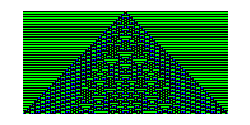
```mathematica
image=-Graphics-;
```

```mathematica
myKeys="Private and Public Keys Association";
```

```mathematica
myAddress=BlockchainKeyEncode[myKeys["PublicKey"],"Address"];
```

To get a preview of the NFT without submitting the transaction to the blockchain, use the "Preview" option:

```mathematica
MintNFT[<|
"Name"-> "My First NFT",
"Thumbnail"-> ImageResize[image,100],
"Source"->image,
"Description"->"Minting my first NFT"
|>,
<|"OwnerAddress"->myAddress ,
"PrivateKey"-> myKeys["PrivateKey"]
|>,"Preview"->True]//Dataset
```

-Graphics-

```mathematica
%["BlockchainTransaction"]
```

BlockchainTransaction[…]

## Source & Additional Information

### Contributed By

Piero Sanchez and Christian Pasquel

### Keywords

blockchain

cryptocurrency

NFT

non-fungible token

cardano

liveminting

### Categories

Cloud & Deployment

Financial Data & Computation

Just For Fun

### Related Symbols

BlockchainData

BlockchainBlockData

BlockchainTransactionData

BlockchainTokenData

BlockchainTransaction

### Related Resource Objects

RandomBlockchainBlockData

WordsFromBitcoinBlockchain

### Source/Reference Citation

Source, reference or citation information

### Links

Cardano Testnet Faucet

### Tests

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

The current implementation of MintNFT only works with the Cardano blockchain. Future versions will support other blockchains.

## Submission Notes

Additional information for the reviewer.